### Start choosing the example:

```mathematica
t=5;
beta=0;
A=0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5},Adjacency Matrix→{{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1},{0,0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{5,U1}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,U1->15}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 2.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.013587,Null}

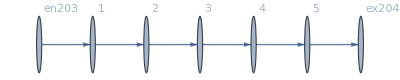

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j205→80.,j206→80.,j207→80.,j208→80.,j209→80.,j210→80.,j211→0.,j212→0.,j213→0.,j214→0.,j215→0.,j216→0.,jt217→0.,jt218→80.,jt219→80.,jt220→0.,jt221→80.,jt222→0.,jt223→80.,jt224→0.,jt225→80.,jt226→0.,u227→335.,u228→255.,u229→175.,u230→95.,u231→15.,u232→335.,u233→255.,u234→175.,u235→95.,u236→15.,u237→15.,u238→335.|>

#### Non-linear case

```mathematica
alpha=0;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

<|j205→80,j206→80,j207→80,j208→80,j209→80,j210→80,j211→0.,j212→0.,j213→0.,j214→0.,j215→0.,j216→0.,jt217→0.,jt218→80,jt219→80,jt220→0.,jt221→80,jt222→0.,jt223→80,jt224→0.,jt225→80,jt226→0.,u227→25.3278,u228→22.7459,u229→20.1639,u230→17.582,u231→15.,u232→25.3278,u233→22.7459,u234→20.1639,u235→17.582,u236→15.,u237→15.,u238→25.3278|>

```mathematica
alpha=0.1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

<|j205→80,j206→80,j207→80,j208→80,j209→80,j210→80,j211→0.,j212→0.,j213→0.,j214→0.,j215→0.,j216→0.,jt217→0.,jt218→80,jt219→80,jt220→0.,jt221→80,jt222→0.,jt223→80,jt224→0.,jt225→80,jt226→0.,u227→27.6454,u228→24.484,u229→21.3227,u230→18.1613,u231→15.,u232→27.6454,u233→24.484,u234→21.3227,u235→18.1613,u236→15.,u237→15.,u238→27.6454|>

```mathematica
alpha=0.3;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

<|j205→80,j206→80,j207→80,j208→80,j209→80,j210→80,j211→0.,j212→0.,j213→0.,j214→0.,j215→0.,j216→0.,jt217→0.,jt218→80,jt219→80,jt220→0.,jt221→80,jt222→0.,jt223→80,jt224→0.,jt225→80,jt226→0.,u227→35.0956,u228→30.0717,u229→25.0478,u230→20.0239,u231→15.,u232→35.0956,u233→30.0717,u234→25.0478,u235→20.0239,u236→15.,u237→15.,u238→35.0956|>

```mathematica
alpha=1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,
SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.7053×10^-13,ComplexInfinity]

<|j205→80,j206→80,j207→80,j208→80,j209→80,j210→80,j211→0.,j212→0.,j213→0.,j214→0.,j215→0.,j216→0.,jt217→0.,jt218→80,jt219→80,jt220→0.,jt221→80,jt222→0.,jt223→80,jt224→0.,jt225→80,jt226→0.,u227→335.,u228→255.,u229→175.,u230→95.,u231→15.,u232→335.,u233→255.,u234→175.,u235→95.,u236→15.,u237→15.,u238→335.|>

```mathematica
alpha=1.2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.00219×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.00219×10^-16

<|j205→80,j206→80,j207→80,j208→80,j209→80,j210→80,j211→0.,j212→0.,j213→0.,j214→0.,j215→0.,j216→0.,jt217→0.,jt218→80,jt219→80,jt220→0.,jt221→80,jt222→0.,jt223→80,jt224→0.,jt225→80,jt226→0.,u227→1470.62,u228→1106.72,u229→742.811,u230→378.906,u231→15.,u232→1470.62,u233→1106.72,u234→742.811,u235→378.906,u236→15.,u237→15.,u238→1470.62|>

```mathematica
alpha=1.6;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j205→80,j206→80,j207→80,j208→80,j209→80,j210→80,j211→0.,j212→0.,j213→0.,j214→0.,j215→0.,j216→0.,jt217→0.,jt218→80,jt219→80,jt220→0.,jt221→80,jt222→0.,jt223→80,jt224→0.,jt225→80,jt226→0.,u227→1.16019×10^6,u228→870144.,u229→580101.,u230→290058.,u231→15.,u232→1.16019×10^6,u233→870144.,u234→580101.,u235→290058.,u236→15.,u237→15.,u238→1.16019×10^6|>

```mathematica
alpha=1.7;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.38879×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.38879×10^-16

<|j205→80,j206→80,j207→80,j208→80,j209→80,j210→80,j211→0.,j212→0.,j213→0.,j214→0.,j215→0.,j216→0.,jt217→0.,jt218→80,jt219→80,jt220→0.,jt221→80,jt222→0.,jt223→80,jt224→0.,jt225→80,jt226→0.,u227→6.238×10^7,u228→4.6785×10^7,u229→3.119×10^7,u230→1.5595×10^7,u231→15.,u232→6.238×10^7,u233→4.6785×10^7,u234→3.119×10^7,u235→1.5595×10^7,u236→15.,u237→15.,u238→6.238×10^7|>

```mathematica
alpha=1.8;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.17196×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.17196×10^-16

<|j205→80,j206→80,j207→80,j208→80,j209→80,j210→80,j211→0.,j212→0.,j213→0.,j214→0.,j215→0.,j216→0.,jt217→0.,jt218→80,jt219→80,jt220→0.,jt221→80,jt222→0.,jt223→80,jt224→0.,jt225→80,jt226→0.,u227→9.62104×10^10,u228→7.21578×10^10,u229→4.81052×10^10,u230→2.40526×10^10,u231→15.,u232→9.62104×10^10,u233→7.21578×10^10,u234→4.81052×10^10,u235→2.40526×10^10,u236→15.,u237→15.,u238→9.62104×10^10|>

```mathematica
alpha=1.9;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.82736×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.82736×10^-16

<|j205→80,j206→80,j207→80,j208→80,j209→80,j210→80,j211→0.,j212→0.,j213→0.,j214→0.,j215→0.,j216→0.,jt217→0.,jt218→80,jt219→80,jt220→0.,jt221→80,jt222→0.,jt223→80,jt224→0.,jt225→80,jt226→0.,u227→2.24148×10^19,u228→1.68111×10^19,u229→1.12074×10^19,u230→5.6037×10^18,u231→15.,u232→2.24148×10^19,u233→1.68111×10^19,u234→1.12074×10^19,u235→5.6037×10^18,u236→15.,u237→15.,u238→2.24148×10^19|>

```mathematica
alpha=2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.84774×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.84774×10^-16

<|j205→80,j206→80,j207→80,j208→80,j209→80,j210→80,j211→0.,j212→0.,j213→0.,j214→0.,j215→0.,j216→0.,jt217→0.,jt218→80,jt219→80,jt220→0.,jt221→80,jt222→0.,jt223→80,jt224→0.,jt225→80,jt226→0.,u227→8.81959×10^106,u228→6.61469×10^106,u229→4.4098×10^106,u230→2.2049×10^106,u231→15.,u232→8.81959×10^106,u233→6.61469×10^106,u234→4.4098×10^106,u235→2.2049×10^106,u236→15.,u237→15.,u238→8.81959×10^106|>